### ArcTan warmup

```mathematica
T = Chop[{{0.0000000000000000,-0.50000000000000000*I},{1.0000000000000000,0.78539816339744828+0.34657359027997264*I}}]
```

{{0,0.-0.5 ⅈ},{1.,0.785398+0.346574 ⅈ}}

```mathematica
M = Chop[{{1.0000000000000000,3.1415926535897931+2.4815418376590830*^-23*I},{0.0000000000000000,1.0000000000000000-9.8943776643499800*^-23*I}}]
```

{{1.,3.14159},{0,1.}}

```mathematica
op[f_, x_] := (x^2+1)D[f,{x,2}]+2x D[f, x];
```

```mathematica
frob = Series[Expand[(x-x0)^s(an (x-x0)^n + an1(x-x0)^(n+1) + an2(x-x0)^(n+2))], {x, x0, 10}]/.{x0->0,s->0}
```

an x^n+an1 x^(1+n)+an2 x^(2+n)

```mathematica
op[frob,x]//FullSimplify
%/(x^(-2+n) )//FullSimplify
Collect[%,x]
```

x^(-2+n) (an n (-1+n+(1+n) x^2)+x (2 an2 x+(an1 (1+n)+an2 (3+n) x) (n+(2+n) x^2)))

an n (-1+n+(1+n) x^2)+x (2 an2 x+(an1 (1+n)+an2 (3+n) x) (n+(2+n) x^2))

-an n+an n^2+an1 n (1+n) x+(2 an2+an n (1+n)+an2 n (3+n)) x^2+an1 (1+n) (2+n) x^3+an2 (2+n) (3+n) x^4

```mathematica
Series[-2z/(z^2+1), {z, 0, 10}]//Simplify
```

-2 z+2 z^3-2 z^5+2 z^7-2 z^9+O[z]^11

```mathematica
Series[ArcTan[x], {x, 0, 5}]
```

x-x^3/3+x^5/5+O[x]^6

```mathematica
f[x]/.First@DSolve[(x^2+1) f''[x]+2 x f'[x]==0,f[x],x]/.{C[1]->f1, C[2]->f0}
```

f0+f1 ArcTan[x]

```mathematica
ArcTan[x]//TrigToExp
```

1/2 ⅈ Log[1-ⅈ x]-1/2 ⅈ Log[1+ⅈ x]

```mathematica
Series[f0+f1(1/2 ⅈ Log[1-ⅈ x]-1/2 ⅈ Log[1+ⅈ x]), {x, I, 10}]/.{f0->0}
```

1/2 ⅈ (f1 Log[2]-f1 Log[ⅈ (-ⅈ+x)])+1/4 f1 (x-ⅈ)+1/16 ⅈ f1 (x-ⅈ)^2-1/48 f1 (x-ⅈ)^3-1/128 ⅈ f1 (x-ⅈ)^4+1/320 f1 (x-ⅈ)^5+1/768 ⅈ f1 (x-ⅈ)^6-(f1 (x-ⅈ)^7)/1792-(ⅈ f1 (x-ⅈ)^8)/4096+(f1 (x-ⅈ)^9)/9216+(ⅈ f1 (x-ⅈ)^10)/20480+O[x-ⅈ]^11

```mathematica
ⅈ (-ⅈ+x)//ExpandAll
```

1+ⅈ x

```mathematica
(Log[I]-Log[2])/2/I//N
```

0.785398+0.346574 ⅈ

```mathematica
-I/2Log[3]//N
```

0.-0.549306 ⅈ

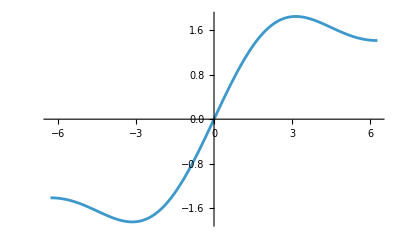

```mathematica
Plot[SinIntegral[x],{x,-2Pi,2Pi}]
```

```mathematica
3 Zeta[2]//N
```

4.9348

```mathematica
-2Pi/3Zeta[2]//N
```

-3.44514

```mathematica
4/9(PolyGamma[1,1/3]-4Zeta[2])//N
```

1.5626